```mathematica
Cmat = ({{Cxx, Cxy}, {Cxy, Cyy}});
```

### For positive tau:

```mathematica
assume = {σ > 0, τ > 0, Cxx > 0, Cxx > 0, Cxx*Cyy > Cxy^2};
ExprPosTau = FullSimplify[Integrate[1/(2π √Det[Cmat])Exp[-1/2{(x - xx) - μx + τ, y - μy}.Inverse[Cmat].{(x - xx) - μx + τ, y - μy}] 1/τ Exp[-xx/τ],{xx, 0, ∞}, Assumptions->assume], assume]
```

(ⅇ^(-(Cxy^2-Cxx Cyy+2 Cxy (-y+μy) τ+τ ((y-μy)^2 τ+2 Cyy (x-μx+τ)))/(2 Cyy τ^2)) (1+Erf[(Cxy^2+Cxy (-y+μy) τ+Cyy (-Cxx+τ (x-μx+τ)))/(√2 √(Cyy (-Cxy^2+Cxx Cyy)) τ)]))/(2 √Cyy √(2 π) τ)

### Quick checks: normalization and means

{Cxx→0.8,Cyy→0.6,Cxy→0.2,μx→1.1,μy→-0.2,τ→1.5}

1.

1.1

-0.2

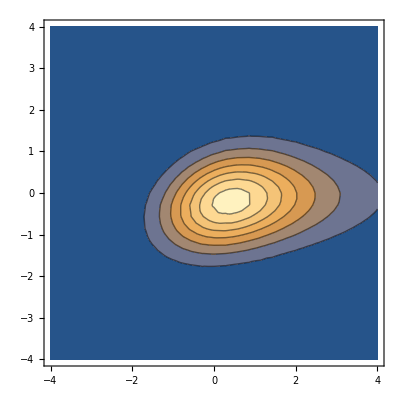

```mathematica
testsubs = {Cxx -> 0.8, Cyy -> 0.6, Cxy -> 0.2, μx -> 1.1, μy -> -0.2, τ -> 1.5}
NIntegrate[ExprPosTau /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}] 
NIntegrate[ExprPosTau*x /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}]
NIntegrate[ExprPosTau*y /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}]

ContourPlot[ExprPosTau /.testsubs, {x, -4, 4}, {y, -4, 4}, PlotRange->All]
```

### For negative tau:

```mathematica
assume = {σ > 0, τ < 0, Cxx > 0, Cxx > 0, Cxx*Cyy > Cxy^2};
ExprNegTau = FullSimplify[Integrate[1/(2π √Det[Cmat])Exp[-1/2{(x - xx) - μx + τ, y - μy}.Inverse[Cmat].{(x - xx) - μx + τ, y - μy}]-1/τ Exp[-xx/τ],{xx, -∞, 0}, Assumptions->assume], assume]
```

-(ⅇ^(-(Cxy^2-Cxx Cyy+2 Cxy (-y+μy) τ+τ ((y-μy)^2 τ+2 Cyy (x-μx+τ)))/(2 Cyy τ^2)) Erfc[(Cxy^2+Cxy (-y+μy) τ+Cyy (-Cxx+τ (x-μx+τ)))/(√2 √(Cyy (-Cxy^2+Cxx Cyy)) τ)])/(2 √Cyy √(2 π) τ)

### Quick checks: normalization and means

{Cxx→0.8,Cyy→0.6,Cxy→0.2,μx→1.1,μy→-0.2,τ→-1.5}

1.

1.1

-0.2

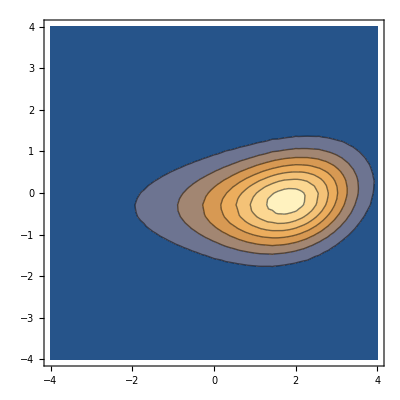

```mathematica
testsubs = {Cxx -> 0.8, Cyy -> 0.6, Cxy -> 0.2, μx -> 1.1, μy -> -0.2, τ -> -1.5}
NIntegrate[ExprNegTau /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}] 
NIntegrate[ExprNegTau*x /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}]
NIntegrate[ExprNegTau*y /.testsubs,{x, -∞, ∞}, {y, -∞, ∞}]

ContourPlot[ExprNegTau /.testsubs, {x, -4, 4}, {y, -4, 4}, PlotRange->All]
```